```mathematica
(***********************************)(*Hyper-parameters (to be tuned!)*)(***********************************)
$jensen=True;(*Jensen or Wasserstein*)
$numposfeatures=0;
$numlatent=16;(*Dimension of the latent space*)$numhiddens=128;(*CNN Hidden Layers*)$depth=2;(*Number of CNN*)$kernelSize=5; (*Look at five grams of characters*)
$batchsize=32;
$discriminatorTerminalTokensQ=True;
$generatorTerminalTokensQ=True;
$updateDiscriminator=1;
(*Other variables*)
ngramInfo = {};
```

```mathematica
(*Use a folder name to dump intermediate results into it*)
$SAVEDIR="/Users/sumansigdel/documents/ChemicalNames";
$device="CPU";

normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"->"",(*Remove gender hints*)
	"-"|"-"|"'"->" ",(*Remove very rare characters*)
	DigitCharacter->"" ,(*Remove very rare characters*)
	"("|")" -> "",(*Remove Brackets*)
	"%"|":" -> "",
"["|"]"->""}(*Remove Colons and %*)];

c = EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[c,StringMatchQ[#,CharacterRange["A","z"]..]&];
```

```mathematica
normalizedChemicalNames = normalizeText@chemicalNames;
```

```mathematica
counts=Counts[StringLength/@normalizedChemicalNames];(*We will use this to generate a realistic length*)
characters=Union[Flatten@Characters@normalizedChemicalNames];
characters2=If[$discriminatorTerminalTokensQ,Join[characters,{StartOfString,EndOfString}],characters];

netpreproc=NetEncoder[{"Characters",characters2,"IgnoreCase"->True}];
```

```mathematica
netpreproc
```

NetEncoder[<>]

```mathematica
characters2
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,StartOfString,EndOfString}

```mathematica
characters
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
{"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"}
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
nonlinearityGenerator=ElementwiseLayer[If[#>0,#,0.2*#]&];
nonlinearityDiscriminator=ElementwiseLayer[If[#>0,#,0.2*#]&];

batchnorm=BatchNormalizationLayer[(*"Scaling"->None,"Biases"->None*)"Scaling"->1,"Biases"->0,"Interleaving"->True,LearningRateMultipliers->{"Scaling"->0,"Biases"->0,_->1}];
instancenorm=NormalizationLayer[1,"Scaling"->None,"Biases"->None];
```

```mathematica
normalizationGenerator=batchnorm;
normalizationDiscriminator=batchnorm;
```

```mathematica
convolutionBlock[n_,args___]:=NetChain[{ConvolutionLayer[n,{$kernelSize},"Stride"->{1},PaddingSize->(($kernelSize-1)/2),"Interleaving"->True,args],normalizationDiscriminator,nonlinearityDiscriminator,DropoutLayer[]}];
```

```mathematica
textDiscriminator=NetChain[<|(*Preprocessing:only keep the maximum values*)"keep max only"->NetGraph[{AggregationLayer[Max,-1],ThreadingLayer[If[#1≥#2-1.*^-7,#1,0]&,-1]},{{NetPort["Input"],1}->2}],Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],"aggregate"->AggregationLayer[Mean,1],"dropout"->DropoutLayer[],"classify"->LinearLayer["Real","Weights"->0,"Biases"->None],If[$jensen,"logit"->LogisticSigmoid,Nothing]|>,"Input"->{"Varying",Length[characters2]}];
```

```mathematica
textGenerator=NetChain[<|If[$generatorTerminalTokensQ,(*Append/Prepend EOS/SOS feature vectors*)"add eos/sos latent"->NetGraph[{ArrayLayer[],AppendLayer[],ArrayLayer[],PrependLayer[]},{{NetPort["Input"],1}->2,{2,3}->4}],Nothing],(*Core deep net*)Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],If[$generatorTerminalTokensQ,(*Remove EOS/SOS high level features*)"remove eos/sos prediction"->NetChain[{SequenceRestLayer[],SequenceMostLayer[]}],Nothing],(*Classifier (of characters)*)"classify"->NetMapOperator@LinearLayer[Length[characters](*,"Weights"->0*)],"squash"->SoftmaxLayer[],If[$discriminatorTerminalTokensQ,"add eos/sos onehot proba"->NetGraph[{(*Catenate zero proba for EOS/SOS inside the generated text*)PaddingLayer[{{0,0},{0,2}}],(*Append/Prepend proba of 1 for EOS/SOS at the end/beginning of the generated text (to be in accordance with the discriminator)*)ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]-1],LearningRateMultipliers->None],PrependLayer[],ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]],LearningRateMultipliers->None],AppendLayer[]},{{1,2}->3,{3,4}->5}],Nothing]|>,"Input"->{"n",$numlatent},"Output"->With[{netpostproc=NetDecoder[netpreproc]},(*Capitalize the decoded (lower-case) text*)NetDecoder[{"Function",Function[StringReplace[netpostproc[#],WordBoundary~~c:WordCharacter:>ToUpperCase[c]]]}]]];
```

NetDecoder::extfwarn: Specified function StringReplace[«2»]& appears to require definitions of external symbols (, ). Be aware that the definitions and values of these symbols will not be retained if the net is saved using Export, Put, or DumpSave.

```mathematica
textGenerator
```

NetChain[<>]

```mathematica
characters1 = AssociationThread[
	Join[CharacterRange["a","z"], {StartOfString, EndOfString}]
	-> Range[28]];

computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters1, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters1],n]]
];

findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2];
DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[500],n], computeNGrams[RandomChoice[dataset,500],n]],{n,1,5}];
```

```mathematica
(*Generation of latent random*)
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]->Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],batchSize];
```

```mathematica
randomizeOnehot[onehot_]:=If[$discriminatorTerminalTokensQ,Join[{First@onehot},Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,Rest@Most@onehot],{Last@onehot}],Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,onehot]];
```

```mathematica
sampleGeneration[batchSize_]:=Block[{s,onehot},s=RandomSample[normalizedChemicalNames,batchSize];
onehot=UnitVectorLayer[Length[characters2],"Input"->{Automatic}][netpreproc[s]];
NumericArray[#,"Real32"]&/@Map[randomizeOnehot,onehot]];
```

```mathematica
dataGenerator={Function[<|"Sample"->sampleGeneration[#BatchSize],"Latent"->latentGeneration[#BatchSize]|>],"RoundLength"->Length[normalizedChemicalNames]};
```

```mathematica
gan=NetGANOperator[{textGenerator,textDiscriminator}]
```

NetGANOperator[<>]

```mathematica
$monitoringLatent=SortBy[latentGeneration[10],Length];
monitorGAN[gan_]:=Block[{generator=NetExtract[gan,"Generator"]},Framed@Column[{Framed@Grid[Transpose@Partition[generator[$monitoringLatent],10],Alignment->Left],Framed@Grid[Transpose@Partition[generator[$monitoringLatent,NetEvaluationMode->"Train"],10],Alignment->Left]}]]

(***********************)
(*Go!!!!!!!!!!!!!!!!!*)
(***********************)

If[$Notebooks,Echo["Training of"->gan]];

If[$SAVEDIR=!=None,CreateDirectory[FileNameJoin[{$SAVEDIR,"monitoring"}],CreateIntermediateDirectories->True]];
trained=NetTrain[gan,dataGenerator,TargetDevice->$device,BatchSize->$batchsize,TrainingUpdateSchedule->{"Discriminator"->$updateDiscriminator,"Generator"},MaxTrainingRounds->100000,TrainingProgressReporting->Append[If[$Notebooks,{{Function[monitorGAN[#Net]],"Interval"->Quantity[1,"Seconds"]},"Panel"},"Print"],If[$SAVEDIR===None,Nothing,File[FileNameJoin[{$SAVEDIR,"training_log.csv"}]]]],TrainingProgressFunction->{Function@Block[{generator},
generator=NetExtract[#Net,"Generator"];
AppendTo[ngramInfo,DistancesofNgrams[generator,normalizedChemicalNames]]],"Interval"->Quantity[1,"Rounds"]},TrainingProgressCheckpointing->If[$SAVEDIR===None,None,{"File",$SAVEDIR<>"/gan.wlnet","Interval"->Quantity[10,"Rounds"]}]];
If[FailureQ[trained],trained,textGenerator=NetExtract[trained,"Generator"]]
```

Training of→NetGANOperator[<>]

CreateDirectory::filex: /Users/sumansigdel/documents/ChemicalNames/monitoring already exists.

$Failed

```mathematica
characters2 // Length
```

28

```mathematica
netpreproc
```

NetEncoder[<>]

```mathematica
Counts@Flatten@Characters@normalizedChemicalNames
```

<|h→2672,y→2356,d→2187,r→3927,o→5980,g→469,e→7799,n→6067,l→4815,i→6153,u→1379,m→2278,t→4223,b→1020,a→5190,p→2221,c→2757,s→1730,w→16,f→766,z→656,x→753,k→67,v→312,q→105,[→12,]→12,j→17|>

```mathematica
Tally[%2099]
```

{{h,2672},{y,2356},{d,2187},{r,3927},{o,5980},{g,469},{e,7799},{n,6067},{l,4815},{i,6153},{u,1379},{m,2278},{t,4223},{b,1020},{a,5190},{p,2221},{c,2757},{s,1730},{w,16},{f,766},{z,656},{x,753},{k,67},{v,312},{q,105},{[,12},{],12},{j,17}}

```mathematica
Drop[<|"h"->2672,"y"->2356,"d"->2187,"r"->3927,"o"->5980,"g"->469,"e"->7799,"n"->6067,"l"->4815,"i"->6153,"u"->1379,"m"->2278,"t"->4223,"b"->1020|>, "m"]
```

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[<|h→2672,y→2356,d→2187,r→3927,o→5980,g→469,e→7799,n→6067,l→4815,i→6153,u→1379,m→2278,t→4223,b→1020|>,m].

Drop[<|h→2672,y→2356,d→2187,r→3927,o→5980,g→469,e→7799,n→6067,l→4815,i→6153,u→1379,m→2278,t→4223,b→1020|>,m]

```mathematica
KeyDrop[Counts@Flatten@Characters@normalizedChemicalNames,{"[","]"}]
```

<|h→2672,y→2356,d→2187,r→3927,o→5980,g→469,e→7799,n→6067,l→4815,i→6153,u→1379,m→2278,t→4223,b→1020,a→5190,p→2221,c→2757,s→1730,w→16,f→766,z→656,x→753,k→67,v→312,q→105,j→17|>

```mathematica
chemicalGAN = Import["/Users/sumansigdel/ChemicalNamesGAN.wlnet"]
```

NetGANOperator[<>]

```mathematica
chemicalGenerator = NetExtract[chemicalGAN,"Generator"]
```

NetChain[<>]

```mathematica
chemicalGenerator@latentChemicalGeneration[100]
```

{Etamete,Pyltafon,Droechedine,Crophretae,Crocathade,Fterycametiadin,Sleorane,Doxin,Daniamine,Dilolesenil,Omenthylameladise,Nlfaninatmlose,Menocorte,Fpfesmltne,Localoidenottaol,Cylprapin,Cropanalolpadoamlthol,Proberriieltalaoaropene,Cinutrphonthylaesdine,Sinuine,Prodenifopirnhyeptne,Phoperie,Pronrane,Pienthadon,Iephoxine,Drachone,Dinougtane,Phose,Dinboccanne,Amlnohyemioe,Dlanenaolinlaromatin,Certphine,Pisrosolthiie,Ltinthynchacoceroxte,Disycaephaloe,Pinalophane,Ameurnsine,Cayrane,Adimior,Doramesdine,Camlorrine,Felcmethil,Alisieertol,Mutylone,Deinlhresine,Tratricentamalon,Pmecinpacyltenie,Ntrine,Dylhexamidine,Seraaline,Lamotocmoprepron,Ulaomenine,Mineatlroprosgltnhyfyl,Oltone,Fesyltriol,Phanidpir,Mrucyshesolychete,Metynirine,Cryrolonolon,Prmide,Crtroseoctrinibil,Lepratrobazopte,Acmidrodinne,Acylthinoleimidene,Nlalepurae,Mideibicinanonine,Ceumbacidhyn,Lopaulon,Pilltesyllethinl,Trmephonyllocoxine,Amine,Losolepane,Sluerion,Bacynnonaiil,Suacthrisirediie,Clephynhocorrodone,Cuoroctane,Ciestxan,Creisolaromltraoxamenallomion,Fuurosan,Meprlinhidlhose,Rhylarestane,Leprine,Cyraphone,Rridatoseloheptocynolane,Diolamidine,Pioe,Ulerhacylate,Ceete,Peptrinin,Doupreetaie,Inataylineane,Lreamutin,Fouratin,Dricamide,Contlrthil,Miteazocrboprrate,Cinillthine,Lliocylloin,Mrexyine}

```mathematica
chemicalDiscriminator = NetExtract[chemicalGAN,"Discriminator"]
```

NetChain[<>]

```mathematica
Max@chemicalDiscriminator@sampleGeneration[1000]
```

0.710305

```mathematica
latentGeneration[1]
```

{NumericArray[…]}

```mathematica
latentChemicalGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]->Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,16}],{-1,1}]],batchSize];
```

```mathematica
latentChemicalGeneration[1]
```

{NumericArray[…]}

```mathematica
counts
```

<|9→144,7→233,8→196,10→57,6→144,5→40,4→11,3→2,11→8,12→1|>

```mathematica
chemicalGenerator
```

NetChain[<>]

```mathematica
Dimensions@distancesLog
```

{401,2}

```mathematica
example = distancesLog[[1]]
```

{10,{0.32535726664229236, 0.15601058065378037, 0.07459857317128638, 0.04126626256015905, 0.03402261102437947}}

```mathematica
example[[2]];
distancesLog[[All,2]];

toInt[n_] := ToExpression[#]&/@StringSplit[StringTrim[n,"{" | "}"],","];

b = distancesLog[[1,2]];
toInt[b];
distancesLogUpdated = toInt[#]&/@ distancesLog[[All,2]];
distancesLogUpdated = MapIndexed[Flatten@Join[{#2 * 10},{#1}]&,distancesLogUpdated]
```

{{10,0.226099,0.134975,0.0748719,0.0453171,0.0334616},{20,0.202532,0.119242,0.0695683,0.0432071,0.0330368},{30,0.189211,0.113366,0.0689132,0.0422898,0.0345452},{40,0.468004,0.343456,0.215485,0.140965,0.0933042},{50,0.422716,0.305482,0.185443,0.111921,0.0716199},{60,0.35648,0.229532,0.129425,0.0786792,0.045713},{70,0.28955,0.165069,0.0851031,0.0499199,0.0344431},{80,0.312185,0.197108,0.110729,0.0641438,0.0387478},{90,0.308744,0.179072,0.0957782,0.0548634,0.0360539},{100,0.273511,0.15967,0.0900204,0.0523721,0.0333969},{110,0.146728,0.0975981,0.0611498,0.0420368,0.0319355},{120,0.27959,0.147311,0.0748005,0.0461417,0.0333596},{130,0.374963,0.227414,0.121053,0.0728843,0.0446356},{140,0.346765,0.235974,0.140611,0.0814292,0.0544006},{150,0.285563,0.193376,0.117606,0.0630345,0.042428},{160,0.217441,0.162091,0.0966813,0.0548597,0.0358334},{170,0.11015,0.0886849,0.0614414,0.0402918,0.0327046},{180,0.158128,0.106859,0.0706274,0.0486477,0.0337363},{190,0.135236,0.0954673,0.065877,0.0448968,0.0316316},{200,0.114779,0.0867037,0.0612986,0.0413835,0.0317249},{210,0.102692,0.0819296,0.0612396,0.0418985,0.0327117},{220,0.115189,0.0892991,0.0586148,0.0409628,0.0318477},{230,0.0883856,0.0818104,0.0564398,0.0383917,0.0323479},{240,0.186678,0.113992,0.0684237,0.0424624,0.031198},{250,0.159456,0.113308,0.0633613,0.0423012,0.0311176},{260,0.176565,0.101697,0.063408,0.0404951,0.0322396},{270,0.381581,0.19564,0.102168,0.0611794,0.041068},{280,0.338496,0.195879,0.130319,0.070157,0.0514501},{290,0.362537,0.238274,0.173405,0.105633,0.0698487},{300,0.226882,0.137493,0.0895774,0.0526431,0.0348166},{310,0.22859,0.164657,0.0940897,0.0571352,0.0365938},{320,0.18775,0.133364,0.0763755,0.0485531,0.0351818},{330,0.211782,0.141752,0.0838726,0.0474752,0.0332394},{340,0.223598,0.136865,0.0759695,0.0478591,0.0347851},{350,0.129476,0.0985319,0.0640721,0.0417698,0.031781},{360,0.225049,0.143006,0.0763994,0.048337,0.0345788},{370,0.224227,0.13424,0.0722619,0.0476865,0.0336081},{380,0.0816998,0.0769055,0.0547855,0.0407328,0.0296819},{390,0.0959457,0.0812709,0.0529729,0.0390908,0.0304104},{400,0.0965077,0.08392,0.056153,0.0407418,0.0300087},{410,0.080859,0.0824298,0.0558236,0.0394335,0.031172},{420,0.162358,0.107214,0.0625371,0.0412373,0.0306454},{430,0.110917,0.0789357,0.0552723,0.0400465,0.0305398},{440,0.261462,0.140358,0.0817412,0.0521628,0.0347841},{450,0.181216,0.109645,0.0638712,0.0435607,0.0316618},{460,0.18877,0.120164,0.0690247,0.0420727,0.0321149},{470,0.232531,0.146859,0.0784663,0.0448457,0.0313911},{480,0.203769,0.127352,0.074884,0.0458122,0.0324051},{490,0.16484,0.125716,0.0735036,0.0458478,0.0343414},{500,0.113304,0.105776,0.0636912,0.0425066,0.0311077},{510,0.109107,0.0947314,0.059858,0.042967,0.0323352},{520,0.11391,0.0874552,0.0559628,0.0399077,0.0327922},{530,0.107902,0.0876607,0.0572378,0.0415736,0.0302342},{540,0.0926838,0.0833917,0.0598157,0.0425104,0.0319304},{550,0.0953466,0.0821566,0.0590655,0.0407344,0.0308695},{560,0.0748501,0.0797773,0.0564626,0.0393015,0.0314965},{570,0.0895629,0.0837622,0.0573126,0.0405068,0.0308473},{580,0.0731298,0.0774269,0.0567408,0.0410266,0.0308989},{590,0.0627514,0.0712434,0.051314,0.0411305,0.0322596},{600,0.067505,0.0686141,0.050832,0.0389572,0.0318224},{610,0.127434,0.0822754,0.0577436,0.0404751,0.0308279},{620,0.0943552,0.0800804,0.0520616,0.0395135,0.0298824},{630,0.0641074,0.0662821,0.0495076,0.0382855,0.0342369},{640,0.0708111,0.0710046,0.0514203,0.0368536,0.0306165},{650,0.070009,0.0701879,0.0504715,0.0386332,0.0323396},{660,0.127484,0.0955727,0.0604433,0.0411742,0.0325799},{670,0.104883,0.0813024,0.054363,0.0406857,0.0318219},{680,0.0752929,0.0700166,0.0528803,0.0382348,0.0323306},{690,0.160054,0.102544,0.0593438,0.0414139,0.033106},{700,0.0684003,0.0678243,0.0470798,0.0374119,0.0320602},{710,0.0796811,0.0725826,0.0506663,0.0375846,0.0307479},{720,0.057047,0.0682265,0.0446423,0.0374774,0.0306199},{730,0.0581446,0.0656924,0.0462636,0.0373272,0.0299365},{740,0.220566,0.141211,0.0830437,0.0528138,0.0351917},{750,0.063547,0.0637557,0.0476952,0.0395423,0.0292662},{760,0.0456169,0.0605128,0.0427434,0.035553,0.0298951},{770,0.05485,0.0560405,0.0452263,0.0377987,0.030398},{780,0.0536015,0.061695,0.0433646,0.0363045,0.0317683},{790,0.0494214,0.0564496,0.0434812,0.0356879,0.030527},{800,0.0515874,0.0625447,0.0456107,0.0364842,0.030435},{810,0.0601647,0.0622279,0.0465232,0.035497,0.0314694},{820,0.0516122,0.0601908,0.0456385,0.0362068,0.0296354},{830,0.0458386,0.0591484,0.0464608,0.0366245,0.0298685},{840,0.0481467,0.0625773,0.0476993,0.0368884,0.0297644},{850,0.0444257,0.0591595,0.0459197,0.0357401,0.032091},{860,0.0457246,0.058607,0.0472722,0.0379394,0.029742},{870,0.0386001,0.0576855,0.0475495,0.0384062,0.0298225},{880,0.0291944,0.0550332,0.044545,0.0344952,0.0319212},{890,0.036228,0.0503299,0.0432797,0.0345392,0.0296629},{900,0.0398095,0.0513067,0.0426588,0.0367418,0.0304106},{910,0.0630878,0.0540164,0.0428582,0.0346396,0.0298088},{920,0.0525318,0.0511925,0.0407275,0.0331133,0.029272},{930,0.0290676,0.0449382,0.0374873,0.0347057,0.0295392},{940,0.0257708,0.0414419,0.0371548,0.0322714,0.0299886},{950,0.0230303,0.035512,0.0355636,0.0349996,0.030221},{960,0.0225382,0.0402974,0.0355704,0.0328222,0.0305556},{970,0.0288419,0.0393483,0.0366671,0.0323277,0.0298747},{980,0.0288698,0.0358979,0.0372004,0.0314875,0.030427},{990,0.0299586,0.0372245,0.0387092,0.0317143,0.030744},{1000,0.023994,0.0385068,0.0379848,0.0336261,0.0281033},{1010,0.0202756,0.0329644,0.0331405,0.031339,0.03001},{1020,0.0151415,0.0340936,0.0361103,0.03296,0.0293555},{1030,0.0277127,0.0336758,0.0344488,0.0312408,0.0308372},{1040,0.0262875,0.0323722,0.0343598,0.0325638,0.0311095},{1050,0.024509,0.0336653,0.0363197,0.0315336,0.0312364},{1060,0.0206542,0.0349878,0.0352281,0.0328254,0.0287421},{1070,0.020018,0.0345629,0.0363771,0.0313978,0.0312775},{1080,0.0198827,0.0342277,0.0334695,0.0323292,0.0317302},{1090,0.0171681,0.0294148,0.0350774,0.0336993,0.0289749},{1100,0.0225814,0.0331022,0.0365783,0.034246,0.0290852},{1110,0.0245343,0.0321681,0.0361538,0.0326746,0.0311318},{1120,0.0212583,0.0323963,0.0343047,0.0325692,0.029408},{1130,0.0253659,0.0336501,0.032918,0.0343953,0.0281009},{1140,0.0174348,0.0337561,0.0343093,0.0328121,0.0282427},{1150,0.0222497,0.0323678,0.0333211,0.0309913,0.0292093},{1160,0.0166741,0.0334164,0.0350165,0.0309545,0.0291703},{1170,0.0167092,0.0299999,0.0354811,0.0321809,0.0295829},{1180,0.0208348,0.0335397,0.0341868,0.0339681,0.0293543},{1190,0.0177325,0.03255,0.0351362,0.0307323,0.0287398},{1200,0.019462,0.0319931,0.0365295,0.0322852,0.029847},{1210,0.0233764,0.0350817,0.0333448,0.0321959,0.0288311},{1220,0.0260871,0.034792,0.0371399,0.0335539,0.0301975},{1230,0.0200835,0.0315339,0.0344467,0.0309388,0.0298243},{1240,0.0179528,0.0371372,0.0360444,0.0338465,0.0297623},{1250,0.0216426,0.0333025,0.0350856,0.0314043,0.0300393},{1260,0.0241073,0.0334897,0.0358474,0.0322933,0.0297879},{1270,0.021896,0.0310778,0.0334316,0.0325899,0.0291567},{1280,0.0207026,0.0320946,0.0358378,0.0312885,0.0286891},{1290,0.0231527,0.0333309,0.0348541,0.0326872,0.0306299},{1300,0.0274001,0.0318255,0.0370736,0.0314072,0.028412},{1310,0.0257671,0.0342509,0.0354127,0.0324587,0.0285059},{1320,0.0220022,0.0360783,0.0347654,0.0349485,0.0291155},{1330,0.0269299,0.0320427,0.0360341,0.0324966,0.028041},{1340,0.0190556,0.0326685,0.0343876,0.0314625,0.0308889},{1350,0.025704,0.0323764,0.0347248,0.0323106,0.0293552},{1360,0.0258926,0.0334884,0.0355944,0.0317521,0.030137},{1370,0.021581,0.0323433,0.0338404,0.0321379,0.0292992},{1380,0.0262271,0.0335338,0.0336552,0.0325365,0.0298208},{1390,0.0249118,0.031025,0.0321664,0.0313687,0.0294932},{1400,0.0200757,0.033543,0.0338378,0.0328305,0.0308379},{1410,0.0191432,0.0316577,0.0341213,0.0315396,0.0292691},{1420,0.0260476,0.0322852,0.0327802,0.0302517,0.030836},{1430,0.0215886,0.0323203,0.0333308,0.0319977,0.0299315},{1440,0.0269554,0.0349876,0.0352612,0.0324617,0.0305432},{1450,0.0242275,0.034178,0.0349913,0.0312563,0.0290145},{1460,0.0238592,0.0301989,0.0345233,0.0297453,0.0294286},{1470,0.0236909,0.0324585,0.0355444,0.0320363,0.0310221},{1480,0.0243835,0.0361563,0.0385421,0.0323082,0.0310307},{1490,0.027016,0.036043,0.0346827,0.0324763,0.0285885},{1500,0.0301566,0.033193,0.0369937,0.0333611,0.0295904},{1510,0.0272373,0.0360302,0.0358295,0.032722,0.0306187},{1520,0.0294391,0.0347202,0.0337134,0.0332172,0.0315529},{1530,0.0256406,0.0340679,0.0363487,0.0319958,0.0289959},{1540,0.0254403,0.0358097,0.036793,0.032264,0.0287279},{1550,0.0316627,0.0351192,0.0333323,0.0318298,0.0297684},{1560,0.0273291,0.0376091,0.0361975,0.0313218,0.0298566},{1570,0.0309772,0.0353387,0.0356296,0.0326951,0.0314109},{1580,0.0298783,0.0342081,0.0348114,0.0318681,0.0284226},{1590,0.0310392,0.0345744,0.037939,0.0320794,0.0285298},{1600,0.0267432,0.0364658,0.0360164,0.0323606,0.0299332},{1610,0.0214771,0.0353483,0.0332351,0.0324423,0.0284742},{1620,0.0273847,0.0356257,0.0369806,0.032198,0.0286852},{1630,0.0303869,0.032101,0.0374681,0.0328166,0.0294774},{1640,0.0331669,0.0378532,0.0360456,0.0336794,0.0299863},{1650,0.0298842,0.0360083,0.0350229,0.0327404,0.0292527},{1660,0.02973,0.0346482,0.0367511,0.0327628,0.0288181},{1670,0.0222907,0.0370936,0.0351901,0.0303037,0.0282826},{1680,0.0284874,0.035301,0.0346181,0.0298472,0.0297793},{1690,0.0286208,0.0384013,0.0358599,0.0330669,0.0309445},{1700,0.0262436,0.0389416,0.0363928,0.033051,0.0293878},{1710,0.02628,0.0360046,0.0365023,0.031806,0.0306876},{1720,0.0208552,0.0327291,0.0373602,0.0312277,0.0314138},{1730,0.0236529,0.0372768,0.036768,0.0336577,0.0307279},{1740,0.032992,0.0335582,0.0351111,0.0349224,0.0293774},{1750,0.0280699,0.0330444,0.0360407,0.0323798,0.0290448},{1760,0.0294348,0.0392969,0.0340409,0.0309798,0.0302968},{1770,0.0273304,0.0380534,0.0329387,0.0317416,0.030644},{1780,0.0305814,0.0337978,0.0356065,0.0327033,0.0294732},{1790,0.0261543,0.0354284,0.0361574,0.0329407,0.0281841},{1800,0.0346823,0.0363419,0.033898,0.0318427,0.0295474},{1810,0.0307591,0.035231,0.0347465,0.0317596,0.029908},{1820,0.0333541,0.0389617,0.0358268,0.0343032,0.0300605},{1830,0.0333637,0.0351478,0.0345467,0.0332169,0.0283926},{1840,0.0286048,0.0377304,0.0354791,0.033078,0.0296475},{1850,0.0270264,0.034186,0.0313425,0.0303417,0.0276486},{1860,0.0276008,0.034561,0.0359088,0.0330361,0.0287987}}

```mathematica
ToExpression[b]
```

{0.226099,0.134975,0.0748719,0.0453171,0.0334616}

{0.325357,0.156011,0.0745986,0.0412663,0.0340226}

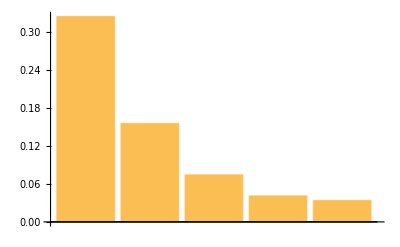

```mathematica
{0.32535726664229236,0.15601058065378037,0.07459857317128638,0.04126626256015905,0.03402261102437947}


BarChart@{0.32535726664229236,0.15601058065378037,0.07459857317128638,0.04126626256015905,0.03402261102437947}
```

```mathematica
StringSplit[example⟦2⟧,","]
```

{{0.32535726664229236, 0.15601058065378037, 0.07459857317128638, 0.04126626256015905, 0.03402261102437947}}

```mathematica
dAWS = Flatten/@distancesLog
```

{{10,{0.2260990191139683, 0.1349752326228955, 0.07487194047004117, 0.04531706082055126, 0.03346157738856893}},{20,{0.20253169930290912, 0.11924150742082033, 0.06956829122257897, 0.043207136611316595, 0.03303678300962365}},{30,{0.18921072865634378, 0.11336558523553047, 0.06891315271472571, 0.04228979173146935, 0.034545199858851}},{40,{0.46800405271950724, 0.3434562304066242, 0.21548530536486143, 0.14096547991729164, 0.09330415256915882}},{50,{0.4227155243087491, 0.3054819325337333, 0.18544271773451326, 0.11192060473869134, 0.07161987524278819}},{60,{0.3564803778844296, 0.2295317287647981, 0.1294251434083561, 0.07867923619228596, 0.04571298371991774}},{70,{0.28954972385316874, 0.16506854295979126, 0.08510305657258711, 0.049919895512399295, 0.03444308032219644}},{80,{0.3121847195482494, 0.19710792700742538, 0.11072920679903928, 0.0641437777587188, 0.03874775752248278}},{90,{0.30874407885035793, 0.17907210345336785, 0.09577820899282043, 0.05486341765874425, 0.036053901597993473}},{100,{0.27351111768901365, 0.15967019697804205, 0.09002035004390635, 0.052372083022105345, 0.033396880938118136}},{110,{0.14672816337168346, 0.09759812976242226, 0.061149841755591884, 0.042036836978939805, 0.031935476176612694}},{120,{0.2795904763788539, 0.14731114091463454, 0.0748005233833552, 0.04614174763671199, 0.03335955988675173}},{130,{0.3749625110203489, 0.22741397972119545, 0.12105279593253099, 0.07288430608411044, 0.04463560036414156}},{140,{0.34676516793831547, 0.23597360835415346, 0.14061060171881273, 0.08142920304640952, 0.05440056712141058}},{150,{0.285563309601295, 0.1933760926327949, 0.11760562527439904, 0.06303450850861032, 0.04242802605897699}},{160,{0.21744143730953114, 0.16209052771924248, 0.09668131414871896, 0.05485969732555146, 0.03583340911643463}},{170,{0.11014996256070188, 0.08868493509047824, 0.061441378912044924, 0.04029180025966621, 0.032704591320949904}},{180,{0.1581277457941898, 0.10685901635361668, 0.07062741765101753, 0.04864768033198152, 0.03373626211253675}},{190,{0.13523578795689067, 0.09546732392922344, 0.06587699286139576, 0.044896846175707286, 0.03163155270074501}},{200,{0.11477929613074422, 0.08670365687885065, 0.061298595962537894, 0.04138352403577516, 0.03172485939081478}},{210,{0.10269174465312361, 0.08192958529748573, 0.06123956383706094, 0.04189847577292683, 0.0327116619105401}},{220,{0.11518928796925867, 0.08929914148668099, 0.05861478874365655, 0.04096280967748873, 0.03184770031785241}},{230,{0.08838564365889366, 0.08181041261742827, 0.05643976788369863, 0.03839171948669164, 0.03234788119414738}},{240,{0.18667755014822218, 0.11399201037653489, 0.06842370859804356, 0.04246237630945854, 0.03119803228188022}},{250,{0.15945586383899568, 0.11330829579090304, 0.06336125252151222, 0.04230123158072107, 0.031117562139521878}},{260,{0.1765650230757286, 0.10169676748393319, 0.06340800429248078, 0.04049510061618469, 0.03223961186856923}},{270,{0.3815809151964511, 0.1956399932453236, 0.10216798435733945, 0.06117936848873423, 0.041068027755003546}},{280,{0.3384959111509623, 0.1958785801406675, 0.13031889599611554, 0.0701570339373712, 0.05145007905149691}},{290,{0.36253659788464315, 0.23827409799050858, 0.17340474764809713, 0.10563346637260793, 0.06984867697244232}},{300,{0.22688151527328299, 0.13749288378219512, 0.08957741413188883, 0.05264309229949257, 0.034816615813014734}},{310,{0.22858954560843747, 0.16465669068397282, 0.09408973756602138, 0.05713520212311275, 0.03659378010387918}},{320,{0.18775048064443683, 0.13336414589328027, 0.0763755147420896, 0.048553092857306156, 0.03518178418401488}},{330,{0.2117820339671984, 0.14175161690903887, 0.08387256467469348, 0.04747516009042695, 0.03323941475060554}},{340,{0.22359758881133163, 0.13686450650200924, 0.0759694819092513, 0.04785912938785893, 0.03478507640157352}},{350,{0.12947568018889893, 0.0985318966481199, 0.06407214557962612, 0.04176979391293986, 0.03178104670659327}},{360,{0.22504932184006157, 0.14300569572525962, 0.07639936077948206, 0.04833696893553188, 0.034578826316577486}},{370,{0.22422651571410673, 0.13423959630877733, 0.07226190241465316, 0.047686463108692866, 0.033608061638085905}},{380,{0.0816997647640306, 0.07690549713117655, 0.05478546665799976, 0.040732787815690764, 0.029681903393754306}},{390,{0.09594570895419179, 0.08127094413292432, 0.05297287347102074, 0.03909082436756195, 0.030410421721435342}},{400,{0.09650768305291543, 0.08392000457737447, 0.05615297178236741, 0.04074176677970945, 0.030008725434297362}},{410,{0.08085896563818638, 0.08242978627852325, 0.05582362759772937, 0.0394334912366537, 0.031171984539092267}},{420,{0.1623580362878938, 0.10721421831707606, 0.06253712547077456, 0.0412373029163375, 0.030645384621098636}},{430,{0.11091704330692936, 0.07893573049492215, 0.05527230154977369, 0.04004646901981357, 0.030539848565837815}},{440,{0.2614617342522637, 0.1403581007083411, 0.08174120571424438, 0.05216280234912912, 0.034784051494829465}},{450,{0.18121573563963786, 0.10964529958713486, 0.06387116107176373, 0.04356070301965822, 0.03166181264833953}},{460,{0.18877014718628415, 0.12016410109516913, 0.06902474342938712, 0.0420727295278639, 0.032114911443905644}},{470,{0.23253147824923875, 0.146858958109986, 0.0784662821038265, 0.04484574987706554, 0.031391132552007234}},{480,{0.20376906258681324, 0.12735169387734027, 0.07488396992092762, 0.04581215702522994, 0.03240513983887187}},{490,{0.16483961499909952, 0.1257164831601369, 0.07350363953169373, 0.04584780884067616, 0.03434136709910393}},{500,{0.11330369499513628, 0.10577643847640555, 0.06369116059206388, 0.042506564829515384, 0.03110766239627177}},{510,{0.1091072271035063, 0.09473135855684964, 0.05985800635576963, 0.04296697830917137, 0.03233520825403282}},{520,{0.11391034467111409, 0.08745519378041869, 0.05596276564050951, 0.039907656845163064, 0.03279224953561227}},{530,{0.10790184527936009, 0.08766065430762748, 0.05723779523997169, 0.04157355528505487, 0.030234205441819956}},{540,{0.09268379715068112, 0.08339167017744184, 0.05981574894736591, 0.0425103722279816, 0.03193044153124211}},{550,{0.09534661851238066, 0.08215658108675356, 0.05906554904632571, 0.04073440438358297, 0.030869476349024462}},{560,{0.07485007425789553, 0.07977734350737385, 0.05646257367557849, 0.03930146254849528, 0.03149653928653313}},{570,{0.08956286061943879, 0.08376219912228526, 0.057312599905777806, 0.040506843383768275, 0.030847295769754354}},{580,{0.07312978942183657, 0.07742688019769936, 0.05674078447261452, 0.041026573972902075, 0.030898946869968788}},{590,{0.06275144545602505, 0.07124338085054509, 0.05131402560671502, 0.04113053577001693, 0.0322595527041488}},{600,{0.06750498058470948, 0.06861414819926244, 0.05083199517853387, 0.0389572439194453, 0.03182242180354616}},{610,{0.12743369017067505, 0.08227536876538162, 0.05774361476304803, 0.040475065074524454, 0.030827865028904104}},{620,{0.09435515619002882, 0.08008037718264699, 0.05206164885295837, 0.03951345070665832, 0.029882364907934077}},{630,{0.06410744263637294, 0.06628208715418783, 0.04950757963249531, 0.03828553471273261, 0.03423687905870378}},{640,{0.0708110800431565, 0.07100460337891458, 0.0514202816079105, 0.036853597715387786, 0.030616454301195094}},{650,{0.07000902090913438, 0.07018794415540311, 0.0504715075920537, 0.03863315104614294, 0.03233961703593922}},{660,{0.1274839657019334, 0.09557270264358231, 0.06044332213582357, 0.04117415278663936, 0.032579884423607194}},{670,{0.10488339599829334, 0.08130239450490025, 0.0543630010351693, 0.040685724707240044, 0.03182189168468402}},{680,{0.07529291697493688, 0.07001661588396245, 0.052880272836672654, 0.03823481295484302, 0.032330636854363354}},{690,{0.1600540394520527, 0.10254430856789688, 0.05934383748858547, 0.04141392398438351, 0.033105952524816726}},{700,{0.06840029224612587, 0.06782429859601663, 0.04707977250534982, 0.03741193541833488, 0.0320602090573387}},{710,{0.0796810863353715, 0.07258256802326087, 0.05066632141111601, 0.037584624620960856, 0.03074793817203588}},{720,{0.05704695044403355, 0.0682265316165619, 0.044642299508447496, 0.03747739495999405, 0.03061994728943909}},{730,{0.058144610544401704, 0.06569241536359019, 0.04626357476606558, 0.03732718109335447, 0.029936507197373636}},{740,{0.2205655219828913, 0.1412114268227961, 0.08304366987478538, 0.05281377342055156, 0.035191666248184504}},{750,{0.06354698564408667, 0.06375571563117942, 0.04769521398805454, 0.03954225618353168, 0.029266232301679813}},{760,{0.04561686751588875, 0.06051281869992653, 0.04274339859746595, 0.035553037999463986, 0.029895089971193372}},{770,{0.054850043233989045, 0.05604053601905548, 0.04522630659826739, 0.03779869576648989, 0.030398006286715643}},{780,{0.053601507267618136, 0.06169503061659669, 0.04336464559557746, 0.03630446253846374, 0.031768336779038384}},{790,{0.04942141127392938, 0.05644957573220762, 0.04348117957439264, 0.035687918350159886, 0.03052697826310049}},{800,{0.051587362621811364, 0.06254466878485346, 0.04561065055720517, 0.036484166226168464, 0.0304350224730493}},{810,{0.06016468601284189, 0.06222787421437302, 0.046523156974089305, 0.035497042621849925, 0.03146944356148529}},{820,{0.05161217215771282, 0.0601907877396688, 0.04563852913979929, 0.036206822000262796, 0.029635418876540243}},{830,{0.04583862734585243, 0.05914844429761116, 0.04646075366057432, 0.03662451666088728, 0.029868544036767593}},{840,{0.048146727850996975, 0.0625772783731192, 0.047699320551546694, 0.036888360497555756, 0.02976440054404366}},{850,{0.04442569213611189, 0.05915954565471058, 0.045919735092545225, 0.035740130354998914, 0.03209103094874269}},{860,{0.04572459655207778, 0.05860699283749094, 0.047272199156261505, 0.037939377960565984, 0.029741967339599478}},{870,{0.03860011785293409, 0.057685509041885984, 0.047549485357370185, 0.03840624916061662, 0.029822485575767572}},{880,{0.029194427868261347, 0.055033217813479, 0.04454504066403361, 0.03449516341167247, 0.03192122346614008}},{890,{0.03622800503778334, 0.050329861172780044, 0.04327967452929167, 0.034539174548975614, 0.02966285324351635}},{900,{0.03980947062550356, 0.051306664768100835, 0.04265883930291046, 0.03674179125700795, 0.030410564586922584}},{910,{0.06308776306077961, 0.05401636625161495, 0.04285822188342867, 0.03463959802806357, 0.02980882771413505}},{920,{0.05253179172665827, 0.051192472227344236, 0.04072745017711165, 0.03311333599718305, 0.029272003757702374}},{930,{0.02906755854673425, 0.0449381978179438, 0.03748732483990152, 0.034705733110963935, 0.029539237236556413}},{940,{0.02577084002023037, 0.041441882665467444, 0.03715484960457078, 0.032271375083586185, 0.029988596717829444}},{950,{0.02303028752791385, 0.03551197032411619, 0.03556355608586026, 0.03499956070856947, 0.030220976495709193}},{960,{0.02253816436591295, 0.04029735621542498, 0.035570363103008984, 0.03282224568117721, 0.03055561786174279}},{970,{0.028841925535236533, 0.03934829195381182, 0.03666712724918114, 0.03232768798754673, 0.02987466998747676}},{980,{0.028869804038361833, 0.035897923049679245, 0.037200419882499385, 0.0314875350005371, 0.030426958757613143}},{990,{0.029958559743509666, 0.03722448875670839, 0.038709198216593625, 0.03171432452007653, 0.03074397269219056}},{1000,{0.023994006887698295, 0.03850679368073357, 0.03798477218541669, 0.03362605954499189, 0.028103269713189986}},{1010,{0.020275605434479954, 0.03296436152653801, 0.033140450860064556, 0.03133896441132809, 0.030009975819868893}},{1020,{0.015141471233128147, 0.034093616559967566, 0.03611031272899773, 0.03296004101460407, 0.029355476364998467}},{1030,{0.027712744971398227, 0.0336757724297444, 0.034448788356860584, 0.0312408062859815, 0.030837244173950656}},{1040,{0.026287533454472274, 0.03237217996437905, 0.03435983904885427, 0.03256376033410424, 0.031109452005803808}},{1050,{0.024508989450540898, 0.033665312248661344, 0.036319714847003276, 0.0315335755895421, 0.03123644843458071}},{1060,{0.02065420063141577, 0.03498779493595088, 0.03522807809934446, 0.03282543746402061, 0.02874211997508152}},{1070,{0.020018008494388197, 0.03456288215001631, 0.03637711151602976, 0.03139778885528201, 0.03127745767385929}},{1080,{0.01988269983647251, 0.0342277389675018, 0.03346946392715558, 0.032329242392721336, 0.03173016716326584}},{1090,{0.017168146373724623, 0.029414799457230932, 0.03507735091737466, 0.03369933249637158, 0.028974937638243176}},{1100,{0.022581437512579794, 0.03310223800385793, 0.03657829160076169, 0.03424596519136146, 0.029085183363391345}},{1110,{0.02453434476199337, 0.03216806115528422, 0.03615378911690848, 0.032674615047307155, 0.031131833407839666}},{1120,{0.021258317557828327, 0.032396250125031334, 0.03430471757877336, 0.03256921286930313, 0.029407970060114082}},{1130,{0.025365890041829327, 0.033650142691641995, 0.03291798296691125, 0.03439534814810948, 0.028100869799260214}},{1140,{0.017434839620395482, 0.03375611915273368, 0.03430928442696952, 0.03281214959139666, 0.028242714093872953}},{1150,{0.02224974235938938, 0.03236777774802985, 0.0333211114200079, 0.03099134823344533, 0.02920930609745125}},{1160,{0.016674120000901006, 0.03341642934386908, 0.03501648925781446, 0.030954540231552582, 0.029170311165316126}},{1170,{0.016709236314842012, 0.02999991953444249, 0.03548106630299712, 0.032180935910872566, 0.029582909488563434}},{1180,{0.020834846614038248, 0.033539729845838126, 0.03418683183896304, 0.03396805791033192, 0.029354263733815777}},{1190,{0.01773252975622349, 0.03254995749697309, 0.035136217598978274, 0.030732310286448954, 0.02873977393706839}},{1200,{0.019461968615779014, 0.03199308104837557, 0.03652948709377921, 0.032285232046666584, 0.02984704659944654}},{1210,{0.023376373446697463, 0.035081675188062704, 0.033344781596600426, 0.03219590671831215, 0.028831077699531363}},{1220,{0.026087061441821366, 0.03479202795619458, 0.03713992786181765, 0.0335539421889057, 0.030197490018664515}},{1230,{0.02008353753612021, 0.031533875011935414, 0.03444673245549329, 0.03093883558232754, 0.029824250752123863}},{1240,{0.017952834248730842, 0.03713724273597801, 0.03604441844749905, 0.03384648564688611, 0.02976225398572467}},{1250,{0.021642555746110865, 0.03330250295129575, 0.03508564070493795, 0.03140425942321998, 0.030039301372362315}},{1260,{0.024107321598322802, 0.03348970634295209, 0.03584740659138122, 0.03229329972692072, 0.029787897481365958}},{1270,{0.021895975225462865, 0.03107782547467, 0.03343158116312118, 0.03258988857632836, 0.029156724049775994}},{1280,{0.0207025661499185, 0.03209458837232058, 0.035837754652980766, 0.031288488486381195, 0.028689139574687328}},{1290,{0.023152738866478402, 0.03333094454096196, 0.03485408704766881, 0.032687244367866575, 0.030629873264038817}},{1300,{0.027400146208057075, 0.03182545550860567, 0.03707363030110236, 0.031407216763406194, 0.02841199265227463}},{1310,{0.025767137399939417, 0.03425090549164783, 0.035412728135892434, 0.03245866044149853, 0.028505949608660142}},{1320,{0.022002159888652735, 0.036078321575339724, 0.034765380545711974, 0.03494853587456945, 0.029115507656186496}},{1330,{0.026929868836665673, 0.032042672145394205, 0.03603413468086788, 0.03249661405707732, 0.02804100578424975}},{1340,{0.019055561001656326, 0.03266852100917197, 0.03438762801226243, 0.03146253034843086, 0.03088886378566609}},{1350,{0.025703997047290556, 0.032376396553125956, 0.034724790028691006, 0.03231058282476354, 0.029355163001964578}},{1360,{0.025892574855938752, 0.03348838483429138, 0.03559438654493117, 0.03175211756852098, 0.03013697978298463}},{1370,{0.021581007042409305, 0.03234330089535489, 0.03384036761819077, 0.032137865251628914, 0.029299238425651433}},{1380,{0.02622707014819192, 0.033533773109957414, 0.03365517769078291, 0.03253649586296913, 0.029820823830647235}},{1390,{0.02491175205148258, 0.03102504387606776, 0.03216635958574468, 0.03136868602575874, 0.029493234831452383}},{1400,{0.020075744325146593, 0.03354300163851221, 0.03383778338276234, 0.032830506682478146, 0.030837892362766475}},{1410,{0.019143154601518414, 0.031657724649447994, 0.03412130180961454, 0.03153961899552619, 0.029269105589492615}},{1420,{0.02604760458832023, 0.032285194983283694, 0.03278015637537693, 0.030251684021920747, 0.030835969960672185}},{1430,{0.021588604399987887, 0.03232025545204776, 0.0333307512489825, 0.03199769551169304, 0.029931462888847765}},{1440,{0.026955402330747724, 0.03498763750634795, 0.035261209742824276, 0.03246170365088866, 0.030543243978972283}},{1450,{0.024227506129894726, 0.03417797822099392, 0.03499127573669736, 0.03125631267634888, 0.029014492248418636}},{1460,{0.023859178077814357, 0.03019892520054436, 0.03452330574417484, 0.02974532727478411, 0.02942857140305676}},{1470,{0.023690888783325318, 0.03245850476923566, 0.03554440218691045, 0.03203633386584933, 0.031022093989520785}},{1480,{0.02438349382731007, 0.036156284878987234, 0.0385421256655185, 0.032308226663868275, 0.031030714952024783}},{1490,{0.027016049299651776, 0.03604302105546247, 0.03468271368074372, 0.03247627108860119, 0.028588529005055926}},{1500,{0.030156562849712465, 0.033193034807862246, 0.03699374430598007, 0.033361124187894164, 0.029590432974236545}},{1510,{0.027237283785854344, 0.03603019773304493, 0.03582945886905743, 0.032722039266060717, 0.030618746035450232}},{1520,{0.029439066110058573, 0.034720216860172286, 0.03371338238638647, 0.033217210765380624, 0.03155288774647003}},{1530,{0.025640595963014674, 0.03406788113690092, 0.03634865691674813, 0.031995801814663744, 0.028995875986834698}},{1540,{0.025440309420594578, 0.03580970618652639, 0.036793006818970415, 0.032263952402128517, 0.028727941130709422}},{1550,{0.03166272149119649, 0.035119234692853586, 0.033332301887068275, 0.031829811701632627, 0.029768383166353368}},{1560,{0.027329108155425476, 0.037609118001689604, 0.036197524997247967, 0.03132184270095438, 0.029856595301724395}},{1570,{0.030977218375823182, 0.03533870246405336, 0.035629637850960155, 0.032695072294146886, 0.031410904068983336}},{1580,{0.02987832773571725, 0.03420807062415829, 0.03481135395013867, 0.031868088441487315, 0.028422595659556477}},{1590,{0.0310391846593195, 0.03457439469227859, 0.0379390296982067, 0.03207937971057152, 0.028529763384350412}},{1600,{0.02674318145615775, 0.036465824463617236, 0.03601643043881596, 0.03236062781113223, 0.029933241766825488}},{1610,{0.021477087273271165, 0.03534827193167381, 0.033235113635282754, 0.032442345204231546, 0.028474232065537758}},{1620,{0.027384747774059512, 0.035625743776918364, 0.03698059767500192, 0.03219796163139765, 0.028685239689547375}},{1630,{0.03038689501150321, 0.03210099251807633, 0.03746811243874976, 0.0328165644919462, 0.029477434057575483}},{1640,{0.033166941334917543, 0.03785315878137831, 0.036045571705581196, 0.033679376005801016, 0.029986348584806165}},{1650,{0.029884188759427333, 0.0360082830159145, 0.03502294210380727, 0.03274038787733047, 0.029252679784346914}},{1660,{0.029729954131720037, 0.034648156180019866, 0.03675111256486913, 0.03276281057983295, 0.028818122669784632}},{1670,{0.02229070920833671, 0.03709363833808162, 0.03519012628009504, 0.03030368495195365, 0.028282579153549894}},{1680,{0.02848735949306258, 0.03530100877176512, 0.03461810827431559, 0.029847150862337985, 0.02977928352565663}},{1690,{0.028620848070154793, 0.038401252160774155, 0.035859863456670374, 0.03306686697864809, 0.030944532103348334}},{1700,{0.026243558466384233, 0.038941589152470646, 0.03639284825544827, 0.033051013670014104, 0.02938775131085925}},{1710,{0.026280017487308963, 0.03600457327163764, 0.0365023084287228, 0.031806002521526135, 0.03068757281572933}},{1720,{0.020855191066426925, 0.03272913679607486, 0.03736017581452018, 0.031227658784393368, 0.03141382402519286}},{1730,{0.023652863295699624, 0.03727683694277461, 0.03676803896198553, 0.03365769273725587, 0.030727910948793364}},{1740,{0.032992037932814994, 0.03355821363187624, 0.03511105756711392, 0.034922370413265576, 0.02937742315469747}},{1750,{0.028069859290420333, 0.03304436710021935, 0.03604070889927255, 0.032379760750567275, 0.029044772651579606}},{1760,{0.029434849783220553, 0.0392968639439163, 0.03404085118710244, 0.030979786173046007, 0.03029678450903406}},{1770,{0.02733041601367903, 0.038053353202564644, 0.032938698650382445, 0.03174161465684565, 0.03064396084741945}},{1780,{0.030581422952557114, 0.03379784343684112, 0.03560653161741409, 0.03270329545924322, 0.029473236723054456}},{1790,{0.026154282958817398, 0.03542837129682884, 0.036157404691020696, 0.03294072803509969, 0.02818412469027578}},{1800,{0.03468225097962705, 0.03634189740431577, 0.03389795051999374, 0.03184273177406037, 0.029547436415658452}},{1810,{0.03075913238708865, 0.03523101701759599, 0.03474654208853105, 0.031759643679270394, 0.029907977732412574}},{1820,{0.03335405043135939, 0.038961682265711464, 0.03582675581196056, 0.03430318702901859, 0.030060512629245025}},{1830,{0.03336371488124037, 0.03514784694424433, 0.0345466737312246, 0.033216942430210755, 0.028392573146736027}},{1840,{0.028604762322051128, 0.037730443710000824, 0.03547909650121857, 0.03307804715404555, 0.0296474626382872}},{1850,{0.02702636405418534, 0.03418601338728452, 0.0313425042806435, 0.03034166608363965, 0.027648561745496174}},{1860,{0.02760081923191458, 0.03456099070632693, 0.035908827698970434, 0.03303607257769543, 0.028798672695045564}}}

```mathematica
Export["DistanceLogAWS.csv", distancesLogUpdated,TableHeadings->{"Round",1,2,3,4,5} ]
```

DistanceLogAWS.csv

```mathematica
ImportedDistance = Import["DistanceLogAWS.csv"];
```

```mathematica
data = Dataset@ImportedDistance
```

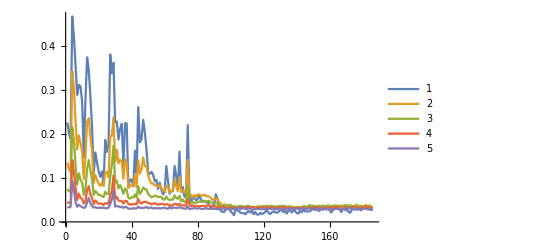

```mathematica
ListLinePlot[Transpose[distancesLogUpdated][[2;;]], PlotLegends->{1,2,3,4,5},PlotRange->All]
```